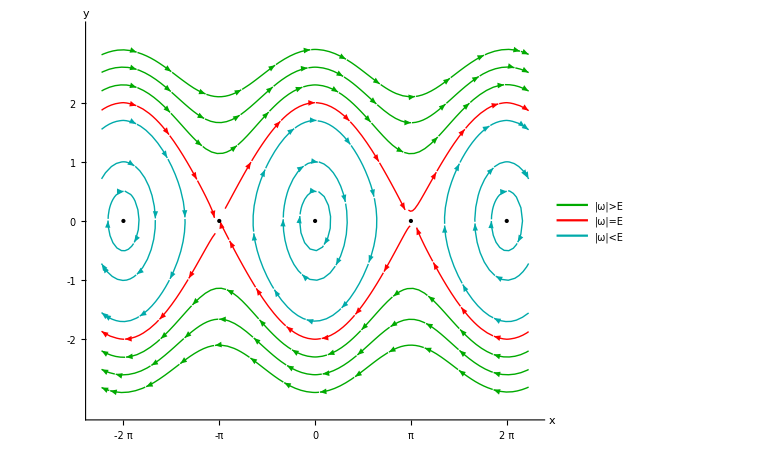

```mathematica
splot = StreamPlot[{y,-Sin[x]},{x,-7,7},{y,-3,3},
AspectRatio->0.8,ImageSize->Large,
Axes->True,AxesLabel->{x,y},Ticks->{{-2Pi, -Pi, 0,Pi,2Pi},{-2,-1,0,1,2}},
Frame->None,
StreamPoints->{{
{{0,-2.9},Green//Darker}, {{0,2.9},Green//Darker},
{{0,-2.6},Green//Darker}, {{0,2.6},Green//Darker},
{{0,-2.3},Green//Darker}, {{0,2.3},Green//Darker},
{{0,-2},Red},{{0,2},Red}, 
{{-2π,-2},Red}, {{-2π,2},Red}, 
{{2π,-2},Red}, {{2π,2},Red},
{{0,1.7},Cyan//Darker}, {{2π,1.7},Cyan//Darker},{{-2π,1.7},Cyan//Darker},
{{0,1},Cyan//Darker}, {{2π,1},Cyan//Darker},{{-2π,1},Cyan//Darker},
{{0,0.5},Cyan//Darker}, {{2π,0.5},Cyan//Darker},{{-2π,0.5},Cyan//Darker}
}},
Epilog->{PointSize->Large,Point[{{0,0},{π,0},{-π,0}, {-2π,0},{2π,0}}]},
PlotLegends->LineLegend[{Green//Darker, Red, Cyan//Darker}, {"|ω|>E","|ω|=E","|ω|<E"}]
]
```

```mathematica
Export["pendulum.pdf", splot]
```

pendulum.pdf